```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ethans/GitHub/161/img

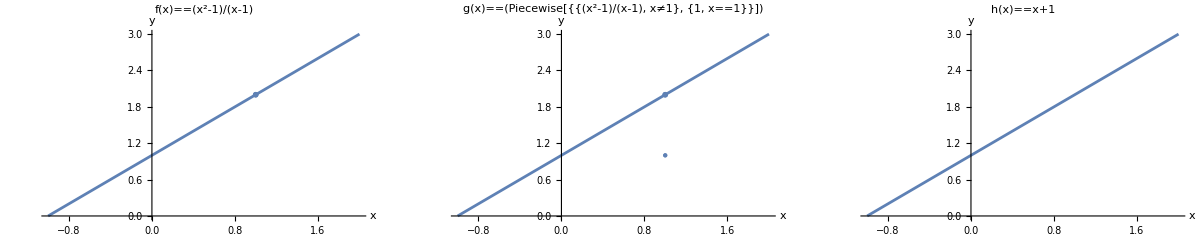

limits-ex1.png

```mathematica
f[x_]=(x^2-1)/(x-1);
{a,b}={-1,2};
c=1;
l=Limit[f[x],x->c];
fplot=Show[
Plot[f[x],{x,a,b},AxesLabel->{x,y},PlotLabel->HoldForm[f[x]]==f[x]],
ListPlot[{{c,l}},PlotMarkers->"OpenMarkers"],
PlotRange->All,ImageSize->Large
];
h[x_]=x+1;
hplot=Plot[h[x],{x,a,b},AxesLabel->{x,y},PlotLabel->HoldForm[h[x]]==h[x],ImageSize->Large,PlotRange->All];

g[x_]=Piecewise[{{f[x],x!=1},{1,x==1}}];
gplot=Show[
Plot[g[x],{x,a,b},AxesLabel->{x,y},PlotLabel->HoldForm[g[x]]==TraditionalForm[g[x]],ImageSize->Large,PlotRange->All],
ListPlot[{{c,l}},PlotMarkers->"OpenMarkers"],
ListPlot[{{c,g[c]}},PlotStyle->PointSize[Large]],
PlotRange->All,ImageSize->Large
];
plt=GraphicsRow[{fplot,gplot,hplot},ImageSize->Full]
Export["limits-ex1.png",plt]
```

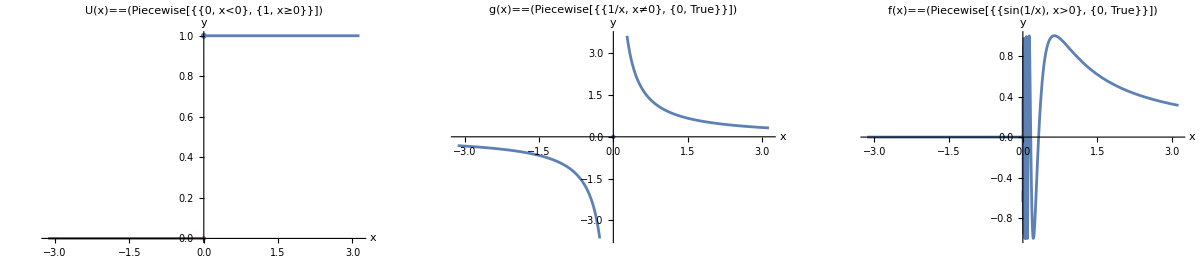

limits-ex2.png

```mathematica
U[x_]=Piecewise[{{0,x<0},{1,x>=0}}];
g[x_]=Piecewise[{{1/x,x!=0},{0,x==0}}];
f[x_]=Piecewise[{{Sin[1/x],x>0},{0,x<=0}}];
{a,b}={-Pi,Pi};
Uplot=Show[
Plot[U[x],{x,a,b},AxesLabel->{x,y},PlotLabel->HoldForm[U[x]]==U[x]],
ListPlot[{{0,0}},PlotStyle->PointSize[Large]],
ListPlot[{{0,1}},PlotMarkers->"OpenMarkers"]
];
gplot=Show[
Plot[g[x],{x,a,b},AxesLabel->{x,y},PlotLabel->HoldForm[g[x]]==g[x]],
ListPlot[{{0,0}},PlotStyle->PointSize[Large]]
];
fplot=Show[
Plot[f[x],{x,a,b},AxesLabel->{x,y},PlotLabel->HoldForm[f[x]]==f[x]],
ListPlot[{{0,0}},PlotStyle->PointSize[Large]]
];
plt=GraphicsRow[{Uplot,gplot,fplot},ImageSize->Full]
Export["limits-ex2.png",plt]
```

```mathematica
Expand[(x+1)*(x-3)*x]
```

-3 x-2 x^2+x^3